```mathematica
1. sea a[n]=3^(|n|)%4, par? impar? periodica? grafica
```

```mathematica
a[n_]:=Mod[3^Abs[n],4]
```

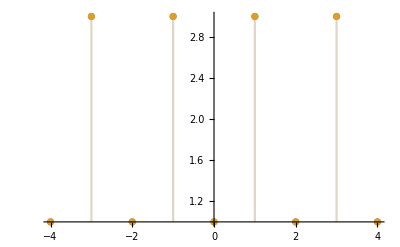

```mathematica
DiscretePlot[{(a[x]),(a[-x])},{x,-4,4}]
```

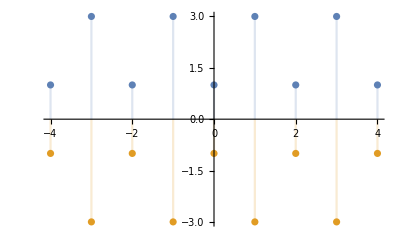

```mathematica
DiscretePlot[{(a[-x]),(-a[x])},{x,-4,4}]
```

```mathematica
2. f(t)=(cos^6)[t+(π/4)] + (sen^6)[3t+(π/2)] par?, impar?, periodica?, serie furier hasta termino 20 (senos,cosenos y compleja)
```

```mathematica
f[t_]:=(Cos[t+(π/4)])^6+(Sin[(3*t)+(π/2)])^6
```

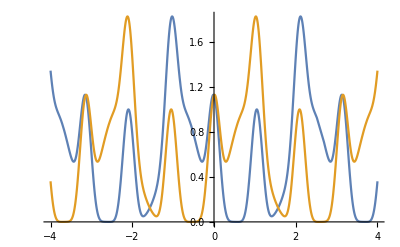

```mathematica
Plot[{f[x],f[-x]},{x,-4,4}]
```

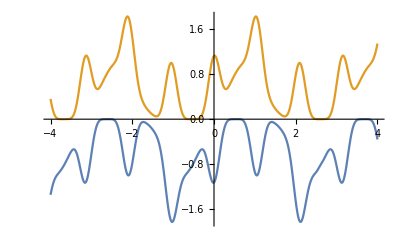

```mathematica
Plot[{-f[x],f[-x]},{x,-4,4}]
```

```mathematica
L=(FunctionPeriod[f[t],t])/2
```

π/2

```mathematica
a0=1/(2*L)∫_-L^L (f[x])ⅆx
```

5/8

```mathematica
a[n_]:=1/L∫_-L^L (f[x]*Cos[(n*x*π)/L])ⅆx
```

```mathematica
b[n_]:=1/L∫_-L^L (f[x]*Sin[(n*x*π)/L])ⅆx
```

```mathematica
sf=a0+∑_(n=1)^10 ((a[n]*Cos[(n*x*π)/L])+(b[n]*Sin[(n*x*π)/L]))
```

5/8-3/16 Cos[4 x]+15/32 Cos[6 x]+3/16 Cos[12 x]+1/32 Cos[18 x]-15/32 Sin[2 x]+1/32 Sin[6 x]

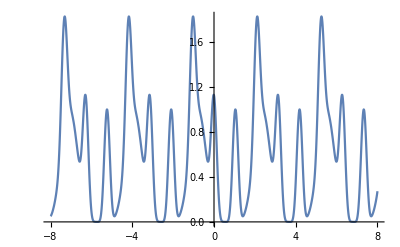

```mathematica
Plot[{sf},{x,-8,8}]
```

```mathematica
c[n_]:=1/L∫_-L^L (f[x]*ⅇ^(-ⅈ*(n*x*π)/L))ⅆx
```

```mathematica
sif=∑_(n=1)^20 c[n]*ⅇ^(ⅈ*(n*x*π)/L)
```

15/32 ⅈ ⅇ^(2 ⅈ x)-3/16 ⅇ^(4 ⅈ x)+(15/32-ⅈ/32) ⅇ^(6 ⅈ x)+3/16 ⅇ^(12 ⅈ x)+1/32 ⅇ^(18 ⅈ x)

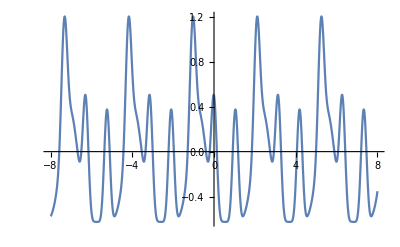

```mathematica
Plot[{Re[sif]},{x,-8,8}]
```

```mathematica
3. g(t)=cos^6(t) + sen^4(t) par?impar?periodica? serie de fourier compleja hasta 20 con g g' g''
```

```mathematica
g[t_]:=(Cos[t])^6+(Sin[t])^4
```

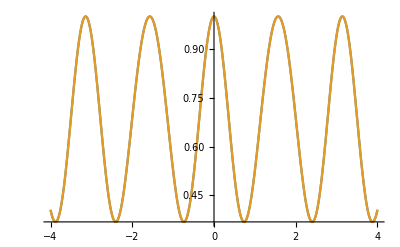

```mathematica
Plot[{g[x],g[-x]},{x,-4,4}]
```

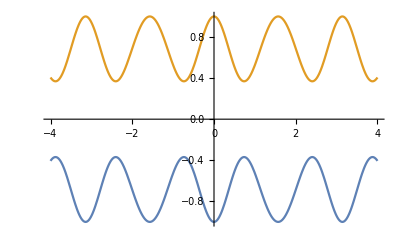

```mathematica
Plot[{-g[x],g[-x]},{x,-4,4}]
```

```mathematica
L=FunctionPeriod[g[t],t]/2
```

π/2

```mathematica
g[x]
```

Cos[x]^6+Sin[x]^4

```mathematica
g'[x]
```

-6 Cos[x]^5 Sin[x]+4 Cos[x] Sin[x]^3

```mathematica
g''[x]
```

-6 Cos[x]^6+12 Cos[x]^2 Sin[x]^2+30 Cos[x]^4 Sin[x]^2-4 Sin[x]^4

```mathematica
c2[n_]:=1/(2*L)∫_-L^L (g[x]*ⅇ^(-ⅈ*(n*x*π)/L))ⅆx
```

```mathematica
sif2=∑_(n=-20)^20 c2[n]*ⅇ^(ⅈ*(n*x*π)/L)
```

11/16-1/64 ⅇ^(-2 ⅈ x)-1/64 ⅇ^(2 ⅈ x)+5/32 ⅇ^(-4 ⅈ x)+5/32 ⅇ^(4 ⅈ x)+1/64 ⅇ^(-6 ⅈ x)+1/64 ⅇ^(6 ⅈ x)

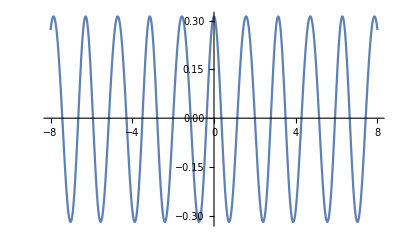

```mathematica
Plot[{Re[sif2]},{x,-8,8}]
```

```mathematica
c2[n_]:=1/(2*L)∫_-L^L (g'[x]*ⅇ^(-ⅈ*(n*x*π)/L))ⅆx
```

```mathematica
sif2=∑_(n=-20)^20 c2[n]*ⅇ^(ⅈ*(n*x*π)/L)
```

1/32 ⅈ ⅇ^(-2 ⅈ x)-1/32 ⅈ ⅇ^(2 ⅈ x)-5/8 ⅈ ⅇ^(-4 ⅈ x)+5/8 ⅈ ⅇ^(4 ⅈ x)-3/32 ⅈ ⅇ^(-6 ⅈ x)+3/32 ⅈ ⅇ^(6 ⅈ x)

```mathematica
c2[n_]:=1/(2*L)∫_-L^L (g''[x]*ⅇ^(-ⅈ*(n*x*π)/L))ⅆx
```

```mathematica
sif2=∑_(n=-20)^20 c2[n]*ⅇ^(ⅈ*(n*x*π)/L)
```

1/16 ⅇ^(-2 ⅈ x)+1/16 ⅇ^(2 ⅈ x)-5/2 ⅇ^(-4 ⅈ x)-5/2 ⅇ^(4 ⅈ x)-9/16 ⅇ^(-6 ⅈ x)-9/16 ⅇ^(6 ⅈ x)

```mathematica
4.; 
f[x_]:= Piecewise[{{-x-1, -2<x<-1},{x+1, -1<x<0},{(x-1)^2,0<x<2}}];
Plot[{f[x]},{x,-2,2}]
```

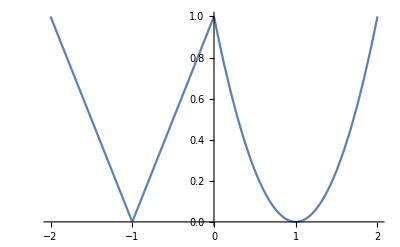
```mathematica
-Graphics-
par? impar? senos, cosenos hasta termino 10, graficar serie
```

```mathematica
L=2
```

2

```mathematica
a0= 1/(2*L)∫_-L^L (f[x])ⅆx
```

5/12

```mathematica
a[n_]:=1/L∫_-L^L (f[x]*Cos[(n*x*π)/L])ⅆx
```

```mathematica
b[n_]:=1/L*∫_-L^L f[x]*Sin[(n*x*π)/L]ⅆx
```

```mathematica
sf=a0+∑_(n=1)^10 (a[n]*Cos[(n*x*π)/L]+b[n]*Sin[(n*x*π)/L])
```

5/12+(4 Cos[π x])/π^2+Cos[2 π x]/(2 π^2)+(4 Cos[3 π x])/(9 π^2)+Cos[4 π x]/(8 π^2)+(4 Cos[5 π x])/(25 π^2)+(4 (-4+π) Sin[(π x)/2])/π^3-(4 (4+3 π) Sin[(3 π x)/2])/(27 π^3)+(4 (-4+5 π) Sin[(5 π x)/2])/(125 π^3)-(4 (4+7 π) Sin[(7 π x)/2])/(343 π^3)+(4 (-4+9 π) Sin[(9 π x)/2])/(729 π^3)

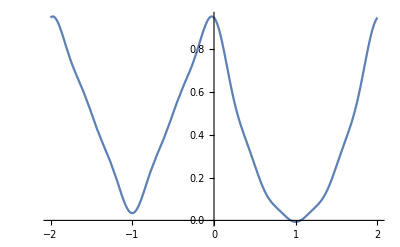

```mathematica
Plot[{sf},{x,-2,2}]
```